# Caso 1

```mathematica
<< "/home/docencia/RRT/RandomData.m"
```

## Apartados 1 y 2

```mathematica
RandomData[]
```

0.773033

```mathematica
max=10000;
```

```mathematica
array=Table[RandomData[],{i,max}];(**)
```

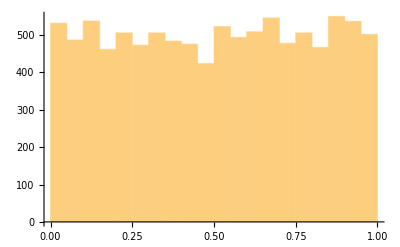

```mathematica
Histogram[array]
```

## Apartado 3

```mathematica
lambda=100;
```

```mathematica
arrayExp=Table[RandomExp[lambda],{i,max}];(*RandomExp es una funcion de Armando que ya tiene en cuenta lo de la dist uniforme*)
```

Histogram::hbins: The bin specification l cannot be used to determine either how many or which bins to use.

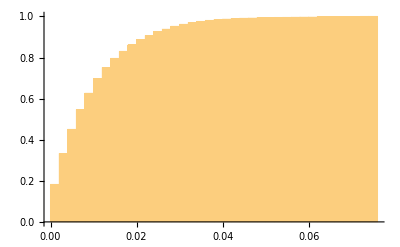

```mathematica
Histogram[arrayExp,l,CDF]
```

```mathematica
(*Para pedir ayuda de una funcion*)
?RandomData`*
```

## Apartado 4

```mathematica
(*Trunca un array entre 50 y 100*)
arrayExp[[50;;100]];
```

```mathematica
(*La media tiene que salir proxima a 1/lambda*)
mean=Mean[arrayExp[[1;;100]]]
```

0.0106145

```mathematica
nmax=10000;
```

```mathematica
InterArr=Table[RandomExp[lambda],nmax];
```

```mathematica
InterArr[[1;;100]];
```

```mathematica
Arriv=Accumulate[InterArr];
```

```mathematica
mu=100;
ServTime=Table[RandomExp[mu],nmax];
ServTime[[1;;11]]
```

{0.022992,0.00264597,0.0152519,0.0141973,0.0154124,0.00626663,0.0270618,0.0066307,0.0126334,0.00796066,0.036155}

```mathematica
(*Module es para organizar la funcion, para que las variables tengan caracter local.
*Primero se definen la variables, luego se inicializan, y finalmente se ejecuta el If.
*El /@ indica que se esta usando un Map[]
*El # es para acceder a cada elemento de la variable arrivals dentro del Map[]
*El &  es para definir una funcion pura, se suele usar con un Map[]  
*)
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
Departures=FifoSchedulling[Arriv,ServTime];
```

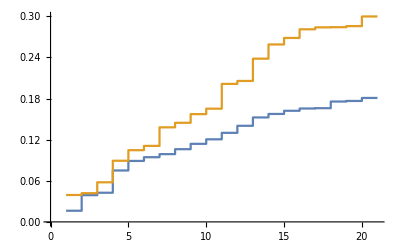

```mathematica
ListStepPlot[{Arriv[[1;;20]],Departures[[1;;20]]}]
```

```mathematica
(*Usar Map[] (sirve para recorrer una lista) en lugar de For[]*)
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,
arrivals]]
```

```mathematica
(*MM/#colas/#usuarios: si hay dos colas y 3 usuarios, cada usuarios ira a una cola,y el tercero se queda esperando*)
```

```mathematica
Manipulate[
ListStepPlot[{Arriv[[origin;;origin+width]],Departures[[origin;;origin+width]]}]
, {origin,1,1000-width,1},{width,10,50,1}
]
```

```mathematica
(*Montañitas: Departures - Arriv
* Necesitas una funcion que te compare los tiempos de llegada con los de salida, de manera que cuando el tiempo de salida sea superior al de llegada, se sume un usuario a la cola*)
```

```mathematica
UsuariosCola[arrivals_, departures_]:= (
Module[{users,n,time,mountain}, users=0;n=1;time=0;mountain={};
For[n=1,n<nmax,n++,If[arrivals[n]> departures[n+1], users++;time=arrivals[n];AppendTo[mountain,{users,time}]]
]
];
Return[mountain]
)
```

{0.016271,0.0389757,0.0425321,0.0750013,0.0889245,0.0943727,0.0988628,0.106059,0.113876,0.120465,0.129917,0.140203,9976,99.172,99.1771,99.1972,99.1999,99.215,99.222,99.2291,99.2441,99.2441,99.2542,99.2809,99.2837}
 |  |  |  |

```mathematica
Apartado 5
```